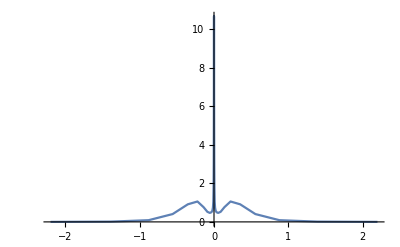

```mathematica
var1 = 46 ; var2 =0;
s=StringForm["/home/cifucito/nrgcode/TwoChNRG/Images/run`1`/rho_`2`_`2`_OmegaRhow.dat",var1,var2];tab = Import[ToString[s],"Table"];ListLinePlot[Transpose[{tab[[All,1]],tab[[All,3]]}],PlotRange->All]
```

46-50
t_2 = 0.02 STATIC
Gamma_2 = 0
U = .5
E = -.25 , -.20 , -.15 , -.10 , -.5

```mathematica
Manipulate[s=StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/run`1`/rho_`2`_`2`_OmegaRhow.dat",Ed2,nDot];tab = Import[ToString[s],"Table"];ListLinePlot[Transpose[{tab[[All,1]],tab[[All,3]]}],PlotRange->{{-2.0,2.0},{0,15.0}},PlotLabel->ToString[StringForm["Ed2 =`1` Dot`2`",-0.25+0.05(Ed2-46),nDot]]],{Ed2,46,50,1},{nDot,0,4,1}]
```

40-45
t_2 = 0.02 STATIC
Gamma_2 = Gamma1
U = .5
E = -.25 , -.20 , -.15 , -.10 , -.5 , .0

```mathematica
Manipulate[s=StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/run`1`/rho_`2`_`2`_OmegaRhow_zEQ1.40.dat",Ed2,nDot];tab = Import[ToString[s],"Table"];ListLinePlot[Transpose[{tab[[All,1]],tab[[All,3]]}],PlotRange->{{-2.0,2.0},{0,15.0}},PlotLabel->ToString[StringForm["Ed2 =`1` Dot`2`",-0.25+0.05(Ed2-40),nDot]]],{Ed2,40,45,1},{nDot,0,4,1}]
```

30-34
t_2 = 0 , 0.005 , 0.01 , 0.015 , 0.02
Gamma_2 = 0
U = E =NOT 0

```mathematica
Manipulate[s=StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/run`1`/rho_`2`_`2`_OmegaRhow.dat",t2,nDot];tab = Import[ToString[s],"Table"];ListLinePlot[Transpose[{tab[[All,1]],tab[[All,3]]}],PlotRange->{{-2.0,2.0},{0,1.0}},PlotLabel->ToString[StringForm["t2 =`1` Dot`2`",0.05(t2-30),nDot]]],{t2,30,34,1},{nDot,0,4,1}]
```

35-39
t_2 = 0 , 0.005 , 0.01 , 0.015 , 0.02
Gamma_2 =Gamma1
U = E =NOT 0

```mathematica
Manipulate[s=StringForm["/home/cifucito/nrgcode/TwoChNRG/Data/run`1`/rho_`2`_`2`_OmegaRhow.dat",t2,nDot];tab = Import[ToString[s],"Table"];ListLinePlot[Transpose[{tab[[All,1]],tab[[All,3]]}],PlotRange->{{-2.0,2.0},{0,15.0}},PlotLabel->ToString[StringForm["t2 =`1` Dot`2`",0.05(t2-35),nDot]]],{t2,35,39,1},{nDot,0,4,1}]
```